```mathematica
f=(#1^2+#2^2-2*#3^2)&;
ffund = (#1^2+#2^2+#3^2)^(-1/2)&;
g1=Grad[f[x,y,z],{x,y,z}]/.{x->#1,y->#2,z->#3} &;
gfund = Table[ffund[##],3] &;
g2 = Table[f[##],3] &;
h=Curl[{ffund[x,y,z],ffund[x,y,z],f[x,y,z]},{x,y,z}]/.{x->#1,y->#2,z->#3} &;
expr=h[x,y,z]
```

{2 y+z/((x^2+y^2+z^2)^(3/2)),-2 x-z/((x^2+y^2+z^2)^(3/2)),-x/((x^2+y^2+z^2)^(3/2))+y/((x^2+y^2+z^2)^(3/2))}

(-13){1,2,3}

```mathematica
a=2;
```

```mathematica
VectorPlot3D[expr,{x,-a,a},{y,-a,a},{z,-a,a}]
```

-Graphics3D-

```mathematica
StreamPlot3D[expr,{x,-a,a},{y,-a,a},{z,-a,a},StreamPoints->Fine]
```

-Graphics3D-

```mathematica
f1=##[[1]]^2+##[[2]]^2-##[[3]]^2&;
ContourPlot3D[f1[{x,y,z}],{x,y,z}∈Ball[{0,0,0},1],Contours->{-0.3,0,0.3},ContourStyle->Opacity[0.8],Mesh->None,RegionBoundaryStyle->None,PlotTheme->"Web"]
```

-Graphics3D-

```mathematica
(* find harmonic vector fields*)
```

```mathematica
Remove["Global`*"]
d=3; (*dimension*)
m=3; (*degree*)
Multiind={};

For[i1=0,i1<=m,i1++,
For[i2=0,i2<=m-i1,i2++,For[i3=0,i3<=m-i2-i1,i3++,Multiind= Union[Multiind,{{i1,i2,i3}}]
]
]
]
Multiind;
alpha = Subscript[a, ##]&;
multiPower=Product[(#1[[i]])^(#2[[i]]),{i,1,d}] &;
poly = Sum[alpha@@ind*multiPower[##,ind],{ind,Multiind}]&;
alphas=Table[alpha@@ind,{ind,Multiind}];

equationSystem={Laplacian[poly[{x,y,z}],{x,y,z}]};

e1={1,0,0};
criticalPointEqns[x0_]:=Module[{eqn,cp=x0},
eqn = Evaluate[Table[D[poly[{x,y,z}],var],{var,{x,y,z}}]/.{x->cp[[1]],y->cp[[2]],z->cp[[3]]}];eqn]

equationSystem = Union[criticalPointEqns[e1],criticalPointEqns[0*e1],equationSystem]

coeffEqns={};
Do[coeffEqns = Union[Union@@Union@@CoefficientList[equation,{x,y,z},Table[m,d]],coeffEqns],
{equation,equationSystem}]
For[i=1,i<=Length[coeffEqns],i++,
	coeffEqns[[i]]=coeffEqns[[i]]==0]

soln = Solve[coeffEqns][[1]];

(*Eliminate free variables*)
freeVars =Union[Select[alphas,!FreeQ[soln[[All,2]],#]&],Complement[alphas,soln[[All,1]]]];
(*freeVars1 = freeVars[[3]];
MapThread[Set,{alphas,alphas/.{freeVars1->1}}];
MapThread[Set,{alphas,alphas/.(##->0& /@ freeVars)}];*)
MapThread[Set,{alphas,alphas/.(##->1& /@ freeVars)}];
(*This part has 2 bugs: the cp-condition is not met, it behaves oddly*)
soln = Solve[coeffEqns][[1]];

(*Map solution to alphas*)
MapThread[Set,{alphas,alphas/. soln}];
poly[{x,y,z}]
```

{a_(0,0,1),a_(0,1,0),a_(1,0,0),a_(0,0,1)+a_(1,0,1)+a_(2,0,1),a_(0,1,0)+a_(1,1,0)+a_(2,1,0),a_(1,0,0)+2 a_(2,0,0)+3 a_(3,0,0),2 a_(0,0,2)+6 z a_(0,0,3)+2 y a_(0,1,2)+2 a_(0,2,0)+2 z a_(0,2,1)+6 y a_(0,3,0)+2 x a_(1,0,2)+2 x a_(1,2,0)+2 a_(2,0,0)+2 z a_(2,0,1)+2 y a_(2,1,0)+6 x a_(3,0,0)}

Set::setraw: Cannot assign to raw object 1.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

1+x^2-(2 x^3)/3+4 x y-4 x^2 y-2 y^2+x y^2+y^3+4 x z-4 x^2 z+y z+x y z+y^2 z+z^2+x z^2+y z^2+z^3

```mathematica
(Grad[poly[{x,y,z}],{x,y,z}]/.{z->0})[[;;2]]
```

{2 x-2 x^2+4 y-8 x y+y^2,4 x-4 x^2-4 y+2 x y+3 y^2}

```mathematica
poly[{x,y,z}]
```

2_(0,0,0)+z 2_(0,0,1)+z^2 2_(0,0,2)+z^3 2_(0,0,3)+y 2_(0,1,0)+y z 2_(0,1,1)+y z^2 2_(0,1,2)+y^2 2_(0,2,0)+y^2 z 2_(0,2,1)+y^3 2_(0,3,0)+x 2_(1,0,0)+x z 2_(1,0,1)+x z^2 2_(1,0,2)+x y 2_(1,1,0)+x y z 2_(1,1,1)+x y^2 2_(1,2,0)+x^2 2_(2,0,0)+x^2 z 2_(2,0,1)+x^2 y 2_(2,1,0)+x^3 2_(3,0,0)

```mathematica
StreamPlot3D[Grad[poly[{x,y,z}],{x,y,z}],{x,y,z}∈Ball[0*e1,2],RegionBoundaryStyle->None,StreamPoints->Fine]
```

-Graphics3D-

```mathematica
regionFunc = ##[[1]]^2+##[[2]]^2+##[[3]]^2&;
k=0;
f1 = Grad[poly[{x,y,z}],{x,y,z}];
colorFunc =Function[{x,y,z,f},ColorData["Rainbow"][Evaluate[(f1.Grad[regionFunc[{xt,yt,zt}],{xt,yt,zt}])/.{xt->x,yt->y,zt->z}]]]
(Function[{x,y,z,f},Evaluate[(f1.Grad[regionFunc[{xt,yt,zt}],{xt,yt,zt}])/.{xt->x,yt->y,zt->z}]])
ContourPlot3D[regionFunc[{x,y,z}], {x,y,z}∈Ball[{0,0,0},3],ColorFunction->colorFunc,Contours->{9},ContourStyle->Opacity[1],Mesh->None,RegionBoundaryStyle->None,PlotTheme->"Web",PerformanceGoal->"Quality",MaxRecursion->4,Mesh->50,EvaluationMonitor->k++]
k
```

Function[{x,y,z,f},ColorData[Rainbow][Evaluate[f1.regionFunc[{xt,yt,zt}]{xt,yt,zt}/.{xt→x,yt→y,zt→z}]]]

Function[{x,y,z,f},2 x (2 x-2 x^2+4 y-8 x y+y^2+4 z-8 x z+y z+z^2)+2 y (4 x-4 x^2-4 y+2 x y+3 y^2+z+x z+2 y z+z^2)+2 z (4 x-4 x^2+y+x y+y^2+2 z+2 x z+2 y z+3 z^2)]

-Graphics3D-

2

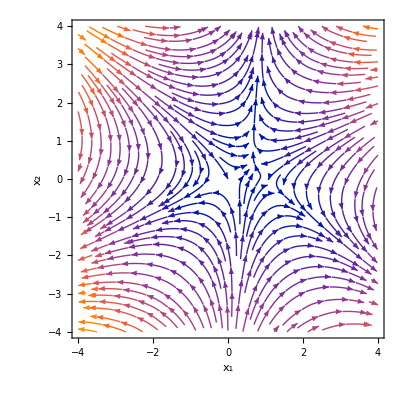

```mathematica
a=4;
StreamPlot[{2 x-2 x^2+4 y-8 x y+y^2,4 x-4 x^2-4 y+2 x y+3 y^2},{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]
```

```mathematica
VectorPlot3D[Evaluate[Grad[poly[{x,y,z}],{x,y,z}]],{x,y,z}∈Ball[0*e1,2],RegionBoundaryStyle->None,VectorPoints->Fine]
```

-Graphics3D-